```mathematica
Flatten[Table[{i,j},{j,2,10},{i,1,j-1}],1]
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6},{1,7},{2,7},{3,7},{4,7},{5,7},{6,7},{1,8},{2,8},{3,8},{4,8},{5,8},{6,8},{7,8},{1,9},{2,9},{3,9},{4,9},{5,9},{6,9},{7,9},{8,9},{1,10},{2,10},{3,10},{4,10},{5,10},{6,10},{7,10},{8,10},{9,10}}

```mathematica
PairPathQ[S_]:=PathGraphQ[Graph[Map[#[[1]]->#[[2]]&,S]]]
```

```mathematica
ithpair[i_]:={i-Floor[(√(8i-7)-1)/2](Floor[(√(8i-7)-1)/2]+1)/2,Ceiling[(√(8i+1)+1)/2]}
```

```mathematica
pairnum[{i_,j_}]:=If[i<j,1+i+1/2(j-3)j,-(1+j+1/2(i-3)i)]
```

```mathematica
Table[pairnum[ithpair[i]],{i,1,10}]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Table[Table[ithpair[i],{i,1,n(n-1)/2}],{n,2,5}]//Column
```

{{1,2}}
{{1,2},{1,3},{2,3}}
{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4}}
{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5}}

```mathematica
allpaths[n_]:=Block[{ss=Subsets[Range[1,n(n-1)/2],{2,n-1}]},
Select[Map[Boole[PairPathQ[Map[ithpair,#]]]*#&,ss],First[#]≠0&]]
```

```mathematica
m=4;
Block[{ss=Subsets[Range[1,m(m-1)/2],{2,m-1}]},
Map[{PadRight[#,m-1],Boole[PairPathQ[Map[ithpair,#]]]}&,ss]]
Expand[InterpolatingPolynomial[%,Table[Subscript[a, i],{i,1,m-1}]]]
```

{{{1,2,0},0},{{1,3,0},1},{{1,4,0},0},{{1,5,0},1},{{1,6,0},0},{{2,3,0},0},{{2,4,0},0},{{2,5,0},0},{{2,6,0},1},{{3,4,0},0},{{3,5,0},0},{{3,6,0},1},{{4,5,0},0},{{4,6,0},0},{{5,6,0},0},{{1,2,3},0},{{1,2,4},0},{{1,2,5},0},{{1,2,6},0},{{1,3,4},0},{{1,3,5},0},{{1,3,6},1},{{1,4,5},0},{{1,4,6},0},{{1,5,6},0},{{2,3,4},0},{{2,3,5},0},{{2,3,6},0},{{2,4,5},0},{{2,4,6},0},{{2,5,6},0},{{3,4,5},0},{{3,4,6},0},{{3,5,6},0},{{4,5,6},0}}

-24-(181 a_1)/6-(97 a_1^2)/12-(11 a_1^3)/6+a_1^4/12+41 a_2+(109 a_1 a_2)/4+25/4 a_1^2 a_2+1/6 a_1^3 a_2-(127 a_2^2)/6-35/4 a_1 a_2^2-3/4 a_1^2 a_2^2+(9 a_2^3)/2+5/6 a_1 a_2^3-a_2^4/3+(163 a_3)/60+(257 a_1 a_3)/90+1/6 a_1^2 a_3+1/36 a_1^3 a_3-(73 a_2 a_3)/18-23/15 a_1 a_2 a_3-1/12 a_1^2 a_2 a_3+41/30 a_2^2 a_3+1/12 a_1 a_2^2 a_3-1/36 a_2^3 a_3+a_3^2/40+1/40 a_1 a_3^2+7/40 a_2 a_3^2+1/5 a_1 a_2 a_3^2-1/5 a_2^2 a_3^2-(3 a_3^3)/40-3/40 a_1 a_3^3+3/40 a_2 a_3^3

```mathematica
Select[allpaths[7],Length[#]==2&]
```

{{1,3},{1,5},{1,8},{1,12},{1,17},{2,6},{2,9},{2,13},{2,18},{3,6},{3,9},{3,13},{3,18},{4,10},{4,14},{4,19},{5,10},{5,14},{5,19},{6,10},{6,14},{6,19},{7,15},{7,20},{8,15},{8,20},{9,15},{9,20},{10,15},{10,20},{11,21},{12,21},{13,21},{14,21},{15,21}}

```mathematica
Column[Sort[Map[Reverse,Out[131]]]]
```

{3,1}
{5,1}
{6,2}
{6,3}
{8,1}
{9,2}
{9,3}
{10,4}
{10,5}
{10,6}
{12,1}
{13,2}
{13,3}
{14,4}
{14,5}
{14,6}
{15,7}
{15,8}
{15,9}
{15,10}
{17,1}
{18,2}
{18,3}
{19,4}
{19,5}
{19,6}
{20,7}
{20,8}
{20,9}
{20,10}
{21,11}
{21,12}
{21,13}
{21,14}
{21,15}

```mathematica
a1==(a+1)
a2==(a+2+b)
b1==(c+1)
b2==(c+2+d)
```

```mathematica
FullSimplify[1+(c+1)+1/2((c+2+d)-3)(c+2+d)]
```

2+c+1/2 (-1+c+d) (2+c+d)

```mathematica
FullSimplify[0<(2+a+1/2 (-1+a+b) (2+a+b))<(2+c+1/2 (-1+c+d) (2+c+d))]
```

0<2+a+1/2 (-1+a+b) (2+a+b)<2+c+1/2 (-1+c+d) (2+c+d)

```mathematica
x==1+(a+1)+1/2((a+2+b)-3)(a+2+b)==(2+a+1/2 (-1+a+b) (2+a+b))
y==1+(c+1)+1/2((c+2+d)-3)(c+2+d)==(2+c+1/2 (-1+c+d) (2+c+d))
0<(2+a+1/2 (-1+a+b) (2+a+b))<(2+c+1/2 (-1+c+d) (2+c+d))
n==1+(2+a+1/2 (-1+a+b) (2+a+b))+1/2((2+c+1/2 (-1+c+d) (2+c+d))-3)(2+c+1/2 (-1+c+d) (2+c+d))
```

```mathematica
{0≤a,
0≤b,
0≤c,
0≤d,
0<(2+a+1/2 (-1+a+b) (2+a+b))<(2+c+1/2 (-1+c+d) (2+c+d)),
n==3+a+1/2 (-1+a+b) (2+a+b)+1/8 (-4+c (3+c)+d+2 c d+d^2) (2+c (3+c)+d+2 c d+d^2)}
```

```mathematica
Reduce[{0≤a,
0≤b,
0≤c,
0≤d,
0<(2+a+1/2 (-1+a+b) (2+a+b))<(2+c+1/2 (-1+c+d) (2+c+d)),
n==3+a+1/2 (-1+a+b) (2+a+b)+1/8 (-4+c (3+c)+d+2 c d+d^2) (2+c (3+c)+d+2 c d+d^2)},Integers]
```

(a|b|c|d|n)∈Integers&&((d==0&&c≥1&&0≤b<-1/2+1/2 √(1+12 c+4 c^2)&&0≤a<1/2 (-3-2 b)+1/2 √(9+8 b+12 c+4 c^2)&&n==1/8 (8+12 a+4 a^2+4 b+8 a b+4 b^2-6 c+7 c^2+6 c^3+c^4))||(d≥1&&c≥0&&0≤b<-1/2+1/2 √(1+12 c+4 c^2+4 d+8 c d+4 d^2)&&0≤a<1/2 (-3-2 b)+1/2 √(9+8 b+12 c+4 c^2+4 d+8 c d+4 d^2)&&n==1/8 (8+12 a+4 a^2+4 b+8 a b+4 b^2-6 c+7 c^2+6 c^3+c^4-2 d+2 c d+14 c^2 d+4 c^3 d-d^2+10 c d^2+6 c^2 d^2+2 d^3+4 c d^3+d^4)))

```mathematica
Simplify[Out[279],0≤a&&0≤b&&0≤c&&0≤d&&(a|b|c|d|n)∈Integers]
```

(d==0&&c≥1&&√(1+12 c+4 c^2)>1+2 b&&√(8 b+(3+2 c)^2)>3+2 a+2 b&&8+12 a+4 a^2+4 b+8 a b+4 b^2+7 c^2+6 c^3+c^4==6 c+8 n)||(d≥1&&√(4 c^2+(1+2 d)^2+4 c (3+2 d))>1+2 b&&√(9+8 b+12 c+4 c^2+4 d+8 c d+4 d^2)>3+2 a+2 b&&8+12 a+4 a^2+4 b+8 a b+4 b^2+7 c^2+6 c^3+c^4+2 c d+14 c^2 d+4 c^3 d+10 c d^2+6 c^2 d^2+2 d^3+4 c d^3+d^4==6 c+2 d+d^2+8 n)

```mathematica
Reduce[0<a1<a2&&0<b1<b2&&0<(1+a1+1/2(a2-3)j)<(1+b1+1/2(b2-3)b2)&&n==1+(1+a1+1/2(a2-3)j)+1/2((1+b1+1/2(b2-3)b2)-3)(1+b1+1/2(b2-3)b2),n,Integers]
```

$Aborted

```mathematica
"The nth position of a pair with difference d is equal to1/2 (2+d^2+(-1+n) n+d (-3+2 n))";
```

```mathematica
#[[2]]-#[[1]]==1&
```

```mathematica
Table[Block[{q3r=Flatten[Position[Table[Boole[#[[2]]-#[[1]]==d&[ithpair[i]]],{i,1,500}],1]]},
{d,CoefficientList[Expand[2*InterpolatingPolynomial[q3r,n]],n]}],{d,1,30}]
```

{{1,{0,1,1}},{2,{0,3,1}},{3,{2,5,1}},{4,{6,7,1}},{5,{12,9,1}},{6,{20,11,1}},{7,{30,13,1}},{8,{42,15,1}},{9,{56,17,1}},{10,{72,19,1}},{11,{90,21,1}},{12,{110,23,1}},{13,{132,25,1}},{14,{156,27,1}},{15,{182,29,1}},{16,{210,31,1}},{17,{240,33,1}},{18,{272,35,1}},{19,{306,37,1}},{20,{342,39,1}},{21,{380,41,1}},{22,{420,43,1}},{23,{462,45,1}},{24,{506,47,1}},{25,{552,49,1}},{26,{600,51,1}},{27,{650,53,1}},{28,{702,55,1}},{29,{756,57,1}},{30,{812,59,1}}}

```mathematica
{d,{(-2+d) (-1+d),1+2 (-1+d),1}}
d->((-2+d) (-1+d)+n(1+2 (-1+d))+n^2)/2
```

```mathematica
FullSimplify[((-2+d) (-1+d)+n(1+2 (-1+d))+n^2)/2]
```

```mathematica
Map[{First[#],Last[#][[2]]}&,Out[253]]
InterpolatingPolynomial[%,d]
```

{{1,1},{2,3},{3,5},{4,7},{5,9},{6,11},{7,13},{8,15},{9,17},{10,19},{11,21},{12,23},{13,25},{14,27},{15,29},{16,31},{17,33},{18,35},{19,37},{20,39},{21,41},{22,43},{23,45},{24,47},{25,49},{26,51},{27,53},{28,55},{29,57},{30,59}}

1+2 (-1+d)

```mathematica
Map[{First[#],Last[#][[1]]}&,Out[253]]
InterpolatingPolynomial[%,d]
```

{{1,0},{2,0},{3,2},{4,6},{5,12},{6,20},{7,30},{8,42},{9,56},{10,72},{11,90},{12,110},{13,132},{14,156},{15,182},{16,210},{17,240},{18,272},{19,306},{20,342},{21,380},{22,420},{23,462},{24,506},{25,552},{26,600},{27,650},{28,702},{29,756},{30,812}}

(-2+d) (-1+d)

```mathematica
Column[%]
```

{1,{0,1,1}}
{2,{0,3,1}}
{3,{2,5,1}}
{4,{6,7,1}}
{5,{12,9,1}}
{6,{20,11,1}}
{7,{30,13,1}}
{8,{42,15,1}}
{9,{56,17,1}}
{10,{72,19,1}}
{11,{90,21,1}}
{12,{110,23,1}}
{13,{132,25,1}}
{14,{156,27,1}}
{15,{182,29,1}}
{16,{210,31,1}}
{17,{240,33,1}}
{18,{272,35,1}}
{19,{306,37,1}}
{20,{342,39,1}}
{21,{380,41,1}}
{22,{420,43,1}}
{23,{462,45,1}}
{24,{506,47,1}}
{25,{552,49,1}}
{26,{600,51,1}}
{27,{650,53,1}}
{28,{702,55,1}}
{29,{756,57,1}}
{30,{812,59,1}}

{2,7,12,13,22,30,31,40,41,42,56,68,69,82,83,84,98,99,100,101,121,138,139,157,158,159,178,179,180,181,201,202,203,204,205}

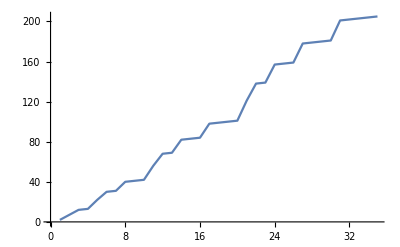

```mathematica
Sort[Map[pairnum,Out[131]]]
ListPlot[%,Joined->True]
```

```mathematica
Sort[Map[Reverse,Out[131]]]
```

{{3,1},{5,1},{6,2},{6,3},{8,1},{9,2},{9,3},{10,4},{10,5},{10,6},{12,1},{13,2},{13,3},{14,4},{14,5},{14,6},{15,7},{15,8},{15,9},{15,10},{17,1},{18,2},{18,3},{19,4},{19,5},{19,6},{20,7},{20,8},{20,9},{20,10},{21,11},{21,12},{21,13},{21,14},{21,15}}

```mathematica
Map[First,Sort[Map[Reverse,Out[131]]]]
Differences[%]
```

{3,5,6,6,8,9,9,10,10,10,12,13,13,14,14,14,15,15,15,15,17,18,18,19,19,19,20,20,20,20,21,21,21,21,21}

{2,1,0,2,1,0,1,0,0,2,1,0,1,0,0,1,0,0,0,2,1,0,1,0,0,1,0,0,0,1,0,0,0,0}

```mathematica
Column[Sort[Map[Reverse,Out[126]]]]
```

{3,1}
{5,1}
{6,2}
{6,3}
{8,1}
{9,2}
{9,3}
{10,4}
{10,5}
{10,6}
{12,1}
{13,2}
{13,3}
{14,4}
{14,5}
{14,6}
{15,7}
{15,8}
{15,9}
{15,10}

```mathematica
Table[Length[allpaths[i]],{i,2,5}]
```

Select::normal: Nonatomic expression expected at position 1 in Select[Null, First[#1] ≠ 0 &].

General::stop: Further output of Select :: normal will be suppressed during this calculation.

{2,2,2,2}

```mathematica
p=3;
Map[And@@#&,Subsets[Range[1,p]]]
```

{True,1,2,3,1&&2,1&&3,2&&3,1&&2&&3}

```mathematica
oneatwlen[x_,n_]:=Normal[SparseArray[x->1,n]]
oneatwlen[2,5]
notat[list_,x_]:=Block[{where=oneatwlen[x,Length[list]]},Table[Piecewise[{{list[[i]], where[[i]]==0}, {!list[[i]], True}}],{i,1,Length[list]}]]
notat[{1,2,3,4,5},2]
onlyat[list_,x_]:=Block[{where=oneatwlen[x,Length[list]]},Table[Piecewise[{{!list[[i]], where[[i]]==0}, {list[[i]], True}}],{i,1,Length[list]}]]
onlyx[list_,x_]:=And@@onlyat[list,x]
onlyx[{1,2,3,4,5},2]
```

{0,1,0,0,0}

{1,!2,3,4,5}

!1&&2&&!3&&!4&&!5

```mathematica
onlyone[L_]:=BooleanConvert[(Or@@Table[onlyx[L,j],{j,1,Length[L]}])||(Map[!#&,And@@L]),"CNF"]
onlyone[{1,2,3,4}]
```

(!1||!2)&&(!1||!3)&&(!1||!4)&&(!2||!3)&&(!2||!4)&&(!3||!4)

```mathematica
nthall[list_,n_]:=And@@Block[{vec=PadLeft[IntegerDigits[n,2],Length[list]]},Table[Piecewise[{{!list[[i]], vec[[i]]==0}, {list[[i]], True}}],{i,1,Length[list]}]]
```

```mathematica
onlyone[Table[nthall[Range[1,5],k],{k,0,2^5-1}]]
```

True

```mathematica
" ∑ p ⊆ E∪E^-1 == #Ps[D]"
```

```mathematica
onlyone[Map[And@@#&,Subsets[{1,2,3,4},{1}]]]
```

(!1||!2)&&(!1||!3)&&(!1||!4)&&(!2||!3)&&(!2||!4)&&(!3||!4)

```mathematica
BooleanConvert[a⊻b⊻c,"DNF"]
```

(a&&b&&c)||(a&&!b&&!c)||(!a&&b&&!c)||(!a&&!b&&c)

```mathematica
Table[Sum[Length[FindPath[CompleteGraph[n],i,j,∞,All]],{i,2,n},{j,1,i-1}],{n,3,8}]
```

{6,30,160,975,6846,54796}



```mathematica
nthor[elist_,n_,len_]:=Graph[Block[{vec=PadLeft[IntegerDigits[n,2],len]},Table[Piecewise[{{elist[[i]][[1]]->elist[[i]][[2]], vec[[i]]==0}, {elist[[i]][[2]]->elist[[i]][[1]], True}}],{i,1,len}]]]
nthor[EdgeList[CompleteGraph[3]],2,3]
```

```mathematica
SumAllPs[g_,vcount_]:=Sum[If[i==j,0,Length[FindPath[g,i,j,∞,All]]],{i,1,vcount},{j,1,vcount}]
allpsor[elist_,n_,elen_,vlen_]:=SumAllPs[nthor[elist,n,elen],vlen]
```

```mathematica
vcounts[g_]:=Block[{elist=EdgeList[g],elen=EdgeCount[g],vlen=VertexCount[g],min=∞,max=-∞},
Do[Block[{thisnum=allpsor[elist,n,elen,vlen]},If[thisnum<min,min=thisnum];If[thisnum>max,max=thisnum]],{n,0,2^elen-1}];max]
Monitor[Table[vcounts[CompleteGraph[q]],{q,3,6}],{q,n}]
```

{6,19,70,237}

```mathematica
vcounts2[g_]:=Block[{elist=EdgeList[g],elen=EdgeCount[g],vlen=VertexCount[g],max=-∞},
Do[Block[{thisnum=allpsor[elist,n,elen,vlen]},If[thisnum>max,max=thisnum]],{n,0,2^elen-1}];max]
```

```mathematica
Monitor[vcounts2[CompleteGraph[7]],n]
```

$Aborted

```mathematica
BooleanConvert[(a&&b&&c)||(!a&&b&&d),"CNF"]
```

(!a||c)&&(a||d)&&b

```mathematica
BooleanConvert[(!a||(b&&c))&&(a||(b&&d)),"CNF"]
```

(!a||c)&&(a||d)&&b

```mathematica
BooleanConvert[((a&&b)||(!a&&c))⧦(b||c),"DNF"]
```

(a&&!c)||(!a&&c)||(b&&c)||(!b&&!c)

```mathematica
BooleanConvert[((a&&b)||(!a&&c)),"CNF"]
```

(!a||b)&&(a||c)

```mathematica
BooleanConvert[(a||b)&&c,"DNF"]
```

(a&&c)||(b&&c)

```mathematica
BooleanConvert[((a1&&c1)||(b1&&c1))&&((a2&&c2)||(b2&&c2))&&((a3&&c3)||(b3&&c3)),"DNF"]
```

(a1&&a2&&a3&&c1&&c2&&c3)||(a1&&a2&&b3&&c1&&c2&&c3)||(a1&&a3&&b2&&c1&&c2&&c3)||(a1&&b2&&b3&&c1&&c2&&c3)||(a2&&a3&&b1&&c1&&c2&&c3)||(a2&&b1&&b3&&c1&&c2&&c3)||(a3&&b1&&b2&&c1&&c2&&c3)||(b1&&b2&&b3&&c1&&c2&&c3)

```mathematica
Exists[x∈X,ForAll[(a,b)∈Subscript[A, x]×Subscript[B, x],a||b]]
```

```mathematica
BooleanConvert[(a1||b1)&&(a2||b2)&&(a3||b3),"DNF"]
```

(a1&&a2&&a3)||(a1&&a2&&b3)||(a1&&a3&&b2)||(a1&&b2&&b3)||(a2&&a3&&b1)||(a2&&b1&&b3)||(a3&&b1&&b2)||(b1&&b2&&b3)

```mathematica
mm=3;
BooleanMinimize[And@@Flatten[Table[(Subscript[a, i]||Subscript[b, j])&&Subscript[c, k],{i,1,mm},{j,1,mm},{k,1,mm}],2],"DNF"]
```

(a_1&&a_2&&a_3&&c_1&&c_2&&c_3)||(b_1&&b_2&&b_3&&c_1&&c_2&&c_3)

```mathematica
SatisfiableQ[(!b||c)&&(a||c)&&(!a||b)&&(!a||!b)&&(a||!b)&&(b||!c)]
```

False

```mathematica
SatisfiableQ[(!a||!b||!c)&&(a||d)&&(a||e)&&(b||d)&&(b||e)&&(c||d)&&(c||e)&&(!d||!e)]
```

False

```mathematica
BooleanConvert[(!x)||(x&&y),"IMPLIES"]
```

x⇒y

```mathematica
BooleanFunction[{{0,0},1},{{0,1},0},{{1,0},
```

```mathematica
ithpair[x]
```

{x-1/2 Floor[1/2 (-1+√(-7+8 x))] (1+Floor[1/2 (-1+√(-7+8 x))]),Ceiling[1/2 (1+√(1+8 x))]}

```mathematica
{a,b}<->{c,d},a==d||b==c
```

```mathematica
conn[{a_,b_},{c_,d_}]:=(a==d||b==c)&&((a≠c)||(b≠d))
```

{{1,2},{1,3},{2,3},{1,4},{2,4},{3,4},{1,5},{2,5},{3,5},{4,5},{1,6},{2,6},{3,6},{4,6},{5,6}}

{3<->1,5<->1,6<->2,6<->3,8<->1,9<->2,9<->3,10<->4,10<->5,10<->6,12<->1,13<->2,13<->3,14<->4,14<->5,14<->6,15<->7,15<->8,15<->9,15<->10}

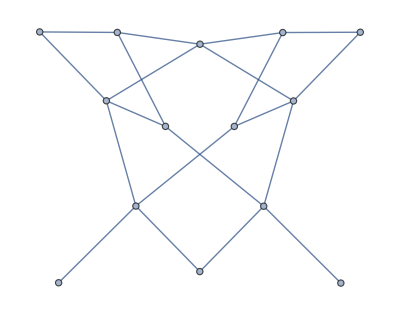

```mathematica
Table[ithpair[i],{i,1,6(6-1)/2}]
Select[Flatten[Table[If[conn[%[[i]],%[[j]]]||conn[%[[j]],%[[i]]],i<->j,1<->1],{i,2,Length[%]},{j,1,i-1}],1],#[[1]]≠1||#[[2]]≠1&]
Graph[%]
```

```mathematica
nonconsecutives[list0_]:=Block[{list={First[list0]},len=Length[list0]},Do[If[list0[[pos]]-list0[[pos-1]]==1,0,AppendTo[list,list0[[pos]]]],{pos,2,len}];list]
Flatten[Position[{1,2,6,1,0,1,1,1,1,2,0,3,0,0,8,1,0,1,0,0,1},0]]
nonconsecutives[%]
```

{5,11,13,14,17,19,20}

{5,11,13,17,19}

```mathematica
1+i+1/2(j-3)j

{1+a,1+a+b},{1+c,1+c+d}
(a==c||a==c+d||a+b==c||a+b==c+d)
(a≠c||a+b≠c+d)
e==1+(1+a)+1/2((1+a+b)-3)(1+a+b)
f==1+(1+c)+1/2((1+c+d)-3)(1+c+d)
```

```mathematica
tolist[x_]:=Table[x[[i]],{i,1,Length[x]}]
```

```mathematica
Expand[(8-32 a+256 a^2+16 (1+a+b)-64 (1+a+b)^2-1024 (1+a+b)^3+4096 (1+a+b)^4+16 c+512 a c-384 (1+a+b) c-1024 (1+a+b)^2 c+16384 (1+a+b)^3 c+192 c^2+1024 (1+a+b) c^2+24576 (1+a+b)^2 c^2+1024 c^3+16384 (1+a+b) c^3+4096 c^4)]
```

3032+13168 a+21696 a^2+15360 a^3+4096 a^4+13200 b+42880 a b+46080 a^2 b+16384 a^3 b+21440 b^2+46080 a b^2+24576 a^2 b^2+15360 b^3+16384 a b^3+4096 b^4+14992 c+47232 a c+48128 a^2 c+16384 a^3 c+46720 b c+96256 a b c+49152 a^2 b c+48128 b^2 c+49152 a b^2 c+16384 b^3 c+25792 c^2+50176 a c^2+24576 a^2 c^2+50176 b c^2+49152 a b c^2+24576 b^2 c^2+17408 c^3+16384 a c^3+16384 b c^3+4096 c^4

```mathematica
Length[DeleteDuplicates[Map[Expand[8*Last[tolist[ReplaceAll[Last[tolist[#]],{C[1]->a,C[2]->b,C[3]->c}]]]]&,tolist[Out[205]]]]]
```

3072

```mathematica
Reduce[{0≤a,0≤b,0≤c,0≤d,
(a==c||a==c+d||a+b==c||a+b==c+d),
(a≠c||a+b≠c+d),
1+(1+(1+a)+1/2((1+a+b)-3)(1+a+b))+1/2(1+(1+c)+1/2((1+c+d)-3)(1+c+d)-3)(1+(1+c)+1/2((1+c+d)-3)(1+c+d))==n},Integers]
```

```mathematica
Monitor[Table[Boole[PathGraphQ[Graph[{#[[1]]<->#[[2]]&[ithpair[ithpair[i][[1]]]],#[[1]]<->#[[2]]&[ithpair[ithpair[i][[2]]]]}]]],{i,1,490000}],i];
Monitor[ArrayPlot[list2spiral[%]],{j,k}]
```

```mathematica
({{43, 44, 45, 46, 47, 48, 49}, {42, 21, 22, 23, 24, 25, 26}, {41, 20, 7, 8, 9, 10, 27}, {40, 19, 6, 1, 2, 11, 28}, {39, 18, 5, 4, 3, 12, 29}, {38, 17, 16, 15, 14, 13, 30}, {37, 36, 35, 34, 33, 32, 31}})
```

```mathematica
Normal[SparseArray[{{1,2}->1,{1,4}->2,{2,1}->3},{4,4}]]//MatrixForm
```

(0 | 1 | 0 | 2
3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
Table[Mod[i-1,4]+1,{i,1,10}]
```

{1,2,3,4,1,2,3,4,1,2}

```mathematica
Clear[n]
```

```mathematica
spiralring[n_]:=Map[If[#==0,0,Mod[#+4n-2,8n]+1+4 (-1+n) n+1]&,Normal[SparseArray[Join[Table[{2n+2-i,1}->i,{i,1,2n+1}],Table[{1,i}->(2n+0+i),{i,1,2n+1}],Table[{i,2n+1}->(4n+i),{i,1,2n+1}],Table[{2n+1,2n+2-i}->(6n+i),{i,1,2n}]],{2n+1,2n+1}]],{2}]
spiral[m_]:=ArrayPad[{{1}},m]+Sum[ArrayPad[spiralring[i],m-i],{i,1,m-1}]+spiralring[m]
spiral[3]//MatrixForm
spiralindices[m_]:=Block[{sp=spiral[m]},Table[First[Position[sp,j]],{j,1,4(m+1-1)(m+1)+1}]]
SparseArray[Table[spiralindices[3][[i]]->i,{i,1,Length[spiralindices[3]]}],{7,7}]//Normal//MatrixForm
list2spiral[list_]:=Block[{si=spiralindices[Ceiling[-1/2+(√(1+Length[list]))/2]]},Normal[SparseArray[Table[si[[k]]->list[[k]],{k,1,Length[list]}]]]]
list2spiral[Range[1,49]]//MatrixForm
```

(43 | 44 | 45 | 46 | 47 | 48 | 49
42 | 21 | 22 | 23 | 24 | 25 | 26
41 | 20 | 7 | 8 | 9 | 10 | 27
40 | 19 | 6 | 1 | 2 | 11 | 28
39 | 18 | 5 | 4 | 3 | 12 | 29
38 | 17 | 16 | 15 | 14 | 13 | 30
37 | 36 | 35 | 34 | 33 | 32 | 31)

(43 | 44 | 45 | 46 | 47 | 48 | 49
42 | 21 | 22 | 23 | 24 | 25 | 26
41 | 20 | 7 | 8 | 9 | 10 | 27
40 | 19 | 6 | 1 | 2 | 11 | 28
39 | 18 | 5 | 4 | 3 | 12 | 29
38 | 17 | 16 | 15 | 14 | 13 | 30
37 | 36 | 35 | 34 | 33 | 32 | 31)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 43 | 44 | 45 | 46 | 47 | 48 | 49
0 | 42 | 21 | 22 | 23 | 24 | 25 | 26
0 | 41 | 20 | 7 | 8 | 9 | 10 | 27
0 | 40 | 19 | 6 | 1 | 2 | 11 | 28
0 | 39 | 18 | 5 | 4 | 3 | 12 | 29
0 | 38 | 17 | 16 | 15 | 14 | 13 | 30
0 | 37 | 36 | 35 | 34 | 33 | 32 | 31)

```mathematica
Reduce[{4 (m) (m+1)==n,m>0,n>0},m]
```

n>0&&m==-1/2+(√(1+n))/2

```mathematica
4(4-1)4+1
```

49

```mathematica
Max[spiral[3]]
```

49

```mathematica
∑_(i=1)^(m-1) 8i
```

4 (-1+m) m

```mathematica
Table[4 (-1+m) m+1,{m,2,5}]
```

{9,25,49,81}

```mathematica
{{2,1+8},{3,1+8+16},{4,1+8+16+24},{5,1+8+16+24+32},{6,1+8+16+24+32}}
```

{{2,9},{3,25},{4,49},{5,81},{6,81}}

```mathematica
InterpolatingPolynomial[{{2,1+8},{3,1+8+16},{4,1+8+16+24},{5,1+8+16+24+32},{6,1+8+16+24+32}},m]
```

9+(16+(4-5/3 (-5+m) (-4+m)) (-3+m)) (-2+m)

```mathematica
FullSimplify[InterpolatingPolynomial[{{1,1},{2,4},{3,7},{4,10}},m]]
```

-2+3 m

```mathematica
FullSimplify[InterpolatingPolynomial[{{2,19},{3,27},{4,35}},m]]
```

3+8 m

```mathematica
Select[Flatten[Table[{{i,j},{k,l}},{i,1,4},{j,1,4},{k,1,4},{l,1,4}],3],Length[DeleteDuplicates[Flatten[#]]]==3&]
```

{{{1,1},{2,3}},{{1,1},{2,4}},{{1,1},{3,2}},{{1,1},{3,4}},{{1,1},{4,2}},{{1,1},{4,3}},{{1,2},{1,3}},{{1,2},{1,4}},{{1,2},{2,3}},{{1,2},{2,4}},{{1,2},{3,1}},{{1,2},{3,2}},{{1,2},{3,3}},{{1,2},{4,1}},{{1,2},{4,2}},{{1,2},{4,4}},{{1,3},{1,2}},{{1,3},{1,4}},{{1,3},{2,1}},{{1,3},{2,2}},{{1,3},{2,3}},{{1,3},{3,2}},{{1,3},{3,4}},{{1,3},{4,1}},{{1,3},{4,3}},{{1,3},{4,4}},{{1,4},{1,2}},{{1,4},{1,3}},{{1,4},{2,1}},{{1,4},{2,2}},{{1,4},{2,4}},{{1,4},{3,1}},{{1,4},{3,3}},{{1,4},{3,4}},{{1,4},{4,2}},{{1,4},{4,3}},{{2,1},{1,3}},{{2,1},{1,4}},{{2,1},{2,3}},{{2,1},{2,4}},{{2,1},{3,1}},{{2,1},{3,2}},{{2,1},{3,3}},{{2,1},{4,1}},{{2,1},{4,2}},{{2,1},{4,4}},{{2,2},{1,3}},{{2,2},{1,4}},{{2,2},{3,1}},{{2,2},{3,4}},{{2,2},{4,1}},{{2,2},{4,3}},{{2,3},{1,1}},{{2,3},{1,2}},{{2,3},{1,3}},{{2,3},{2,1}},{{2,3},{2,4}},{{2,3},{3,1}},{{2,3},{3,4}},{{2,3},{4,2}},{{2,3},{4,3}},{{2,3},{4,4}},{{2,4},{1,1}},{{2,4},{1,2}},{{2,4},{1,4}},{{2,4},{2,1}},{{2,4},{2,3}},{{2,4},{3,2}},{{2,4},{3,3}},{{2,4},{3,4}},{{2,4},{4,1}},{{2,4},{4,3}},{{3,1},{1,2}},{{3,1},{1,4}},{{3,1},{2,1}},{{3,1},{2,2}},{{3,1},{2,3}},{{3,1},{3,2}},{{3,1},{3,4}},{{3,1},{4,1}},{{3,1},{4,3}},{{3,1},{4,4}},{{3,2},{1,1}},{{3,2},{1,2}},{{3,2},{1,3}},{{3,2},{2,1}},{{3,2},{2,4}},{{3,2},{3,1}},{{3,2},{3,4}},{{3,2},{4,2}},{{3,2},{4,3}},{{3,2},{4,4}},{{3,3},{1,2}},{{3,3},{1,4}},{{3,3},{2,1}},{{3,3},{2,4}},{{3,3},{4,1}},{{3,3},{4,2}},{{3,4},{1,1}},{{3,4},{1,3}},{{3,4},{1,4}},{{3,4},{2,2}},{{3,4},{2,3}},{{3,4},{2,4}},{{3,4},{3,1}},{{3,4},{3,2}},{{3,4},{4,1}},{{3,4},{4,2}},{{4,1},{1,2}},{{4,1},{1,3}},{{4,1},{2,1}},{{4,1},{2,2}},{{4,1},{2,4}},{{4,1},{3,1}},{{4,1},{3,3}},{{4,1},{3,4}},{{4,1},{4,2}},{{4,1},{4,3}},{{4,2},{1,1}},{{4,2},{1,2}},{{4,2},{1,4}},{{4,2},{2,1}},{{4,2},{2,3}},{{4,2},{3,2}},{{4,2},{3,3}},{{4,2},{3,4}},{{4,2},{4,1}},{{4,2},{4,3}},{{4,3},{1,1}},{{4,3},{1,3}},{{4,3},{1,4}},{{4,3},{2,2}},{{4,3},{2,3}},{{4,3},{2,4}},{{4,3},{3,1}},{{4,3},{3,2}},{{4,3},{4,1}},{{4,3},{4,2}},{{4,4},{1,2}},{{4,4},{1,3}},{{4,4},{2,1}},{{4,4},{2,3}},{{4,4},{3,1}},{{4,4},{3,2}}}

```mathematica
Tally[Map[ordnum,Permutations[{1,2,3,4,5,6}]]]
Table[{PadLeft[IntegerDigits[BitXor[%[[i]][[1]],%[[i+1]][[1]]],2]],Abs[%[[i]][[2]]-%[[i+1]][[2]]]},{i,1,Length[%]-1}]
```

{{0,1},{1,5},{2,14},{3,10},{4,19},{5,35},{6,26},{7,10},{8,14},{9,40},{10,61},{11,35},{12,26},{13,40},{14,19},{15,5},{16,5},{17,19},{18,40},{19,26},{20,35},{21,61},{22,40},{23,14},{24,10},{25,26},{26,35},{27,19},{28,10},{29,14},{30,5},{31,1}}

{{{1},4},{{1,1},9},{{1},4},{{1,1,1},9},{{1},16},{{1,1},9},{{1},16},{{1,1,1,1},4},{{1},26},{{1,1},21},{{1},26},{{1,1,1},9},{{1},14},{{1,1},21},{{1},14},{{1,1,1,1,1},0},{{1},14},{{1,1},21},{{1},14},{{1,1,1},9},{{1},26},{{1,1},21},{{1},26},{{1,1,1,1},4},{{1},16},{{1,1},9},{{1},16},{{1,1,1},9},{{1},4},{{1,1},9},{{1},4}}

```mathematica
count[bvec_]:=Total[Map[Boole[ords[#]==bvec]&,Permutations[Range[Length[bvec]+1]]]]
```

```mathematica
count[{0,0,0,0,1}]
```

5

```mathematica
Map[count[#]==count[Reverse[not[#]]]&,Map[PadLeft[IntegerDigits[#,2],4]&,Range[0,2^4-1]]]
```

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

```mathematica
Monitor[Table[Block[{l={}},Do[
Block[{vec=PadLeft[IntegerDigits[i,2],mm]},

If[FreeQ[l,not[vec]]&&
FreeQ[l,Reverse[vec]]&&
FreeQ[l,Reverse[not[vec]]],AppendTo[l,vec]]

],{i,0,2^mm-1}];l]//Length,{mm,2,10}],mm]
2^mm
```

{2,3,6,10,20,36,72,136,272}

```mathematica
"A005418";
```

2^mm

```mathematica
mm=7;
DeleteDuplicates[DeleteDuplicates[DeleteDuplicates[Map[PadLeft[IntegerDigits[#,2],mm]&,Range[0,2^mm-1]],#1==Reverse[not[#2]]&],#1==not[#2]&],#1==Reverse[#2]&]
Map[{count[#],FromDigits[#,2],#}&,%]
```

```mathematica
Length[{{0,0,0,0,0,0,0},{0,0,0,0,0,0,1},{0,0,0,0,0,1,0},{0,0,0,0,0,1,1},{0,0,0,0,1,0,0},{0,0,0,0,1,0,1},{0,0,0,0,1,1,0},{0,0,0,0,1,1,1},{0,0,0,1,0,0,0},{0,0,0,1,0,0,1},{0,0,0,1,0,1,0},{0,0,0,1,0,1,1},{0,0,0,1,1,0,0},{0,0,0,1,1,0,1},{0,0,0,1,1,1,0},{0,0,1,0,0,0,1},{0,0,1,0,0,1,0},{0,0,1,0,0,1,1},{0,0,1,0,1,0,0},{0,0,1,0,1,0,1},{0,0,1,0,1,1,0},{0,0,1,1,0,0,1},{0,0,1,1,0,1,0},{0,0,1,1,1,0,0},{0,0,1,1,1,0,1},{0,0,1,1,1,1,0},{0,1,0,0,0,0,1},{0,1,0,0,0,1,0},{0,1,0,0,1,0,1},{0,1,0,0,1,1,0},{0,1,0,1,0,0,1},{0,1,0,1,0,1,0},{0,1,0,1,1,1,0},{0,1,1,0,0,0,1},{0,1,1,0,1,1,0},{0,1,1,1,1,1,0}}]
```

36

```mathematica
mm=6;
Table[Total[Sort[Map[count,Select[Map[PadLeft[IntegerDigits[#,2],mm]&,Range[0,2^mm-1]],Total[#]==j&]]]],{j,0,6}]
```

{1,120,1191,2416,1191,120,1}

```mathematica
mm=7;
Table[Total[Sort[Map[count,Select[Map[PadLeft[IntegerDigits[#,2],mm]&,Range[0,2^mm-1]],Total[#]==j&]]]],{j,0,6}]
```

{1,247,4293,15619,15619,4293,247}

```mathematica
Map[{#[[1]],#[[2]]}&,%]
```

{{1,0},{6,1},{20,2},{15,3},{34,4},{64,5},{50,6},{20,7},{99,9},{155,10},{90,11},{71,12},{111,13},{55,14},{78,17},{169,18},{272,21},{181,22},{132,25},{29,30}}

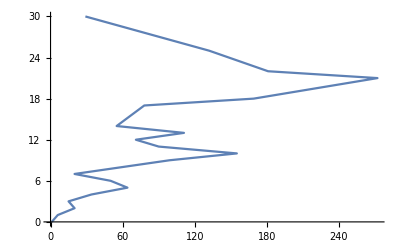

```mathematica
ListPlot[%,Joined->True]
```

```mathematica
{{1,{0,0,0}},{3,{0,0,1}},{5,{0,1,0}}}
```

```mathematica
not[l_]:=Map[1-#&,l]
```

```mathematica
not[{1,1,0,1}]
```

{0,0,1,0}

```mathematica
Map[{#[[2]],PadLeft[IntegerDigits[#[[1]],2],5]}&,%]//Column
```

{1,{0,0,0,0,0}}
{5,{0,0,0,0,1}}
{14,{0,0,0,1,0}}
{10,{0,0,0,1,1}}
{19,{0,0,1,0,0}}
{35,{0,0,1,0,1}}
{26,{0,0,1,1,0}}
{10,{0,0,1,1,1}}
{14,{0,1,0,0,0}}
{40,{0,1,0,0,1}}
{61,{0,1,0,1,0}}
{35,{0,1,0,1,1}}
{26,{0,1,1,0,0}}
{40,{0,1,1,0,1}}
{19,{0,1,1,1,0}}
{5,{0,1,1,1,1}}
{5,{1,0,0,0,0}}
{19,{1,0,0,0,1}}
{40,{1,0,0,1,0}}
{26,{1,0,0,1,1}}
{35,{1,0,1,0,0}}
{61,{1,0,1,0,1}}
{40,{1,0,1,1,0}}
{14,{1,0,1,1,1}}
{10,{1,1,0,0,0}}
{26,{1,1,0,0,1}}
{35,{1,1,0,1,0}}
{19,{1,1,0,1,1}}
{10,{1,1,1,0,0}}
{14,{1,1,1,0,1}}
{5,{1,1,1,1,0}}
{1,{1,1,1,1,1}}

```mathematica
Tally[{1,2,2,3}]
```

{{1,1},{2,2},{3,1}}

```mathematica
obgraph[l_]:=Graph[Table[Piecewise[{{i->(i+1), l[[i]]==0}, {(i+1)->i, True}}],{i,1,Length[l]}]]
```

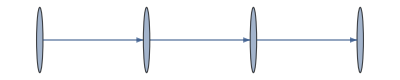
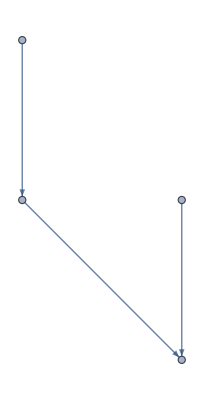
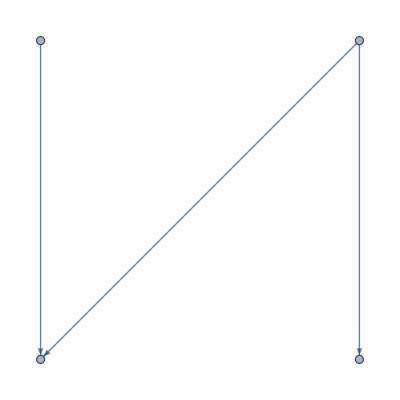
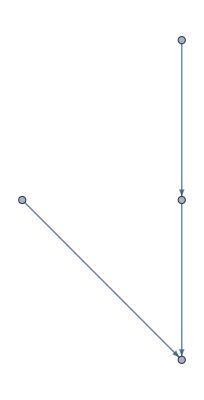
{{0,0,0},-Graphics-}
{{0,0,1},-Graphics-}
{{0,1,0},-Graphics-}
{{0,1,1},-Graphics-}

```mathematica
DeleteDuplicates[Map[{PadLeft[IntegerDigits[#,2],3],obgraph[PadLeft[IntegerDigits[#,2],3]]}&,Range[0,2^2-1]],IsomorphicGraphQ]//Column
```

```mathematica
ordnum[l_]:=FromDigits[ords[l],2]
ordnum[{3,1,2}]
```

2

```mathematica
ords[{3,1,2,4}]
```

{1,0,0}

```mathematica
{3>1<2<4};
Graph[{3->1,2->1,4->2}]
```

-Graphics-

```mathematica
ograph[l_]:=Graph[Table[Piecewise[{{l[[i]]->l[[i+1]], l[[i]]>l[[i+1]]}, {l[[i+1]]->l[[i]], True}}],{i,1,Length[l]-1}]]
```

```mathematica
ords[l_]:=Table[Boole[l[[i]]>l[[i+1]]],{i,1,Length[l]-1}]
```

```mathematica
deg2rad[x_]:=FullSimplify[x*π/180]
rad2deg[x_]:=FullSimplify[(x*180)/π]
```

```mathematica
Map[deg2rad,{150,-315,144,-30π}]
```

{(5 π)/6,-(7 π)/4,(4 π)/5,-π^2/6}

```mathematica
(150*π)/180==(15π)/18==(5π)/6
```

```mathematica
Map[rad2deg,{5π/2,-2π/5,-7π/12,5/18}]
```

{450,-72,-105,50/π}

```mathematica
Map[{Cos[#],Sin[#]}&,{-5π/3}]
```

{{1/2,(√3)/2}}

```mathematica
(-19π)/4==(-19π)/4+2π==(-19π)/4+(16π)/4==
```

```mathematica
FullSimplify[TrigExpand[Cos[ArcCos[20/29]+20π/3]]]
FullSimplify[TrigExpand[Sin[ArcCos[20/29]+20π/3]]]
```

1/58 (-20-21 √3)

1/58 (-21+20 √3)

```mathematica
Expand[(x+a)(x+b)]
```

a b+a x+b x+x^2

```mathematica
nthor[g_,n_]:=Graph[Block[{vec=PadLeft[IntegerDigits[n,2],EdgeCount[g]],el=EdgeList[g]},Table[Piecewise[{{el[[i]][[1]]->el[[i]][[2]], vec[[i]]==0}, {el[[i]][[2]]->el[[i]][[1]], True}}],{i,1,Length[el]}]]]
```

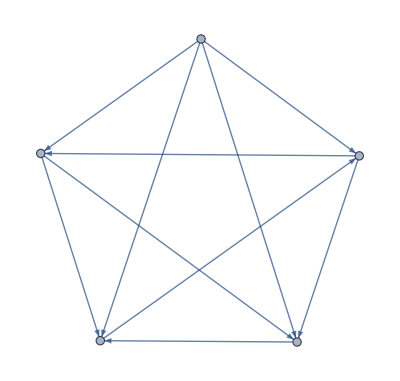

{True,SparseArray[<10>, {5, 5}],{{0,5,4,7,7},{0,0,1,2,3},{0,2,0,2,2},{0,1,1,0,1},{0,1,1,2,0}}}

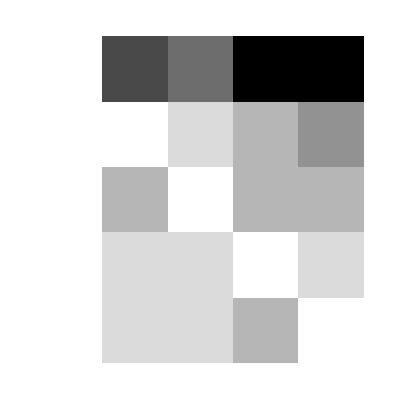
{True,-Graphics-,-Graphics-}

```mathematica
nthor[CompleteGraph[5],8]
{Length[FindCycle[%,∞,All]]>0,AdjacencyMatrix[%],Table[Length[FindPath[%,i,j,∞,All]],{i,1,VertexCount[%]},{j,1,VertexCount[%]}]}
{%[[1]],ArrayPlot[%[[2]]],ArrayPlot[%[[3]]]}
```

```mathematica
Length[First[Out[541]]]
```

904

```mathematica
enum[l_]:=Table[Prepend[l[[qw]],qw],{qw,1,Length[l]}]
```

```mathematica
CGars[n_,x_]:=
Block[{or=nthor[CompleteGraph[n],x]},{Length[FindCycle[or,∞,All]]>0,AdjacencyMatrix[or],Table[Length[FindPath[or,i,j,∞,All]],{i,1,VertexCount[or]},{j,1,VertexCount[or]}]}]
```

```mathematica
c5s=Monitor[Map[Drop[#,1]&,Select[Table[CGars[5,x],{x,0,2^EdgeCount[CompleteGraph[5]]-1}],First]],{x,i,j}];
```

```mathematica
ec5s=enum[c5s];
```

```mathematica
MatrixForm[Last[c5s[[9]]]]
```

(0 | 3 | 3 | 3 | 10
0 | 0 | 1 | 1 | 3
0 | 1 | 0 | 1 | 3
0 | 1 | 1 | 0 | 3
0 | 0 | 0 | 0 | 0)

```mathematica
EdgeList[AdjacencyGraph[First[c5s[[55]]]]]
```

{1->2,1->3,1->4,2->3,2->5,3->4,3->5,4->2,4->5,5->1}

```mathematica
MatrixForm[First[c5s[[55]]]]
```

(0 | 1 | 1 | 1 | 0
0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 1 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0)

```mathematica
EdgeList[CompleteGraph[5]]
```

{1<->2,1<->3,1<->4,1<->5,2<->3,2<->4,2<->5,3<->4,3<->5,4<->5}

```mathematica
"Try new version with top side forward (from orientation)";
"Note that symmetries in even a portion of the adj. mat. gives symmetry in the path matrix.";
```

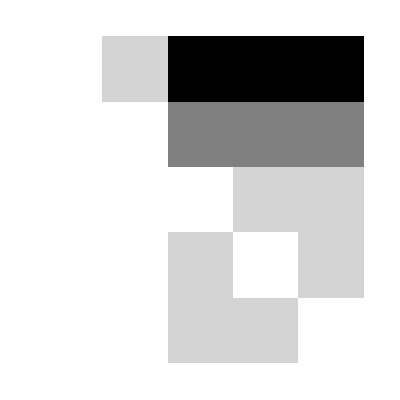
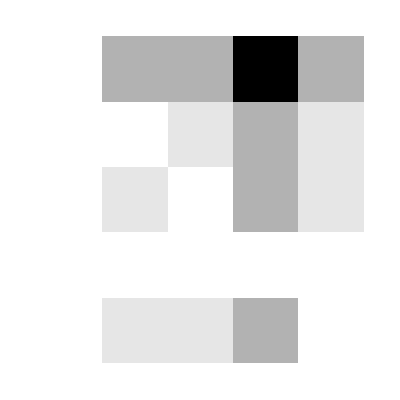
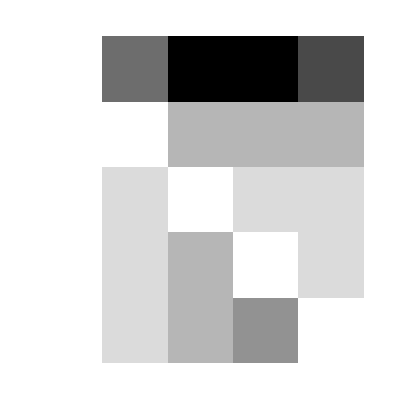
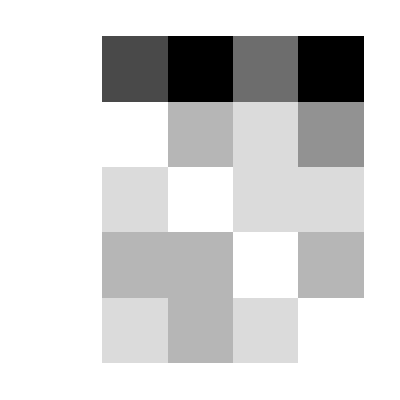
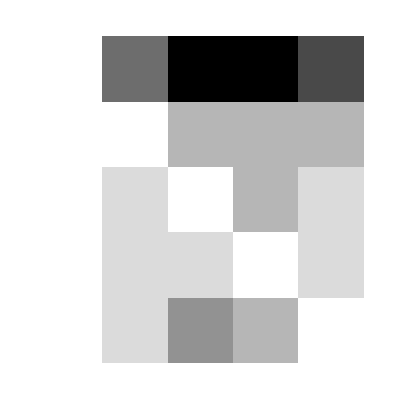
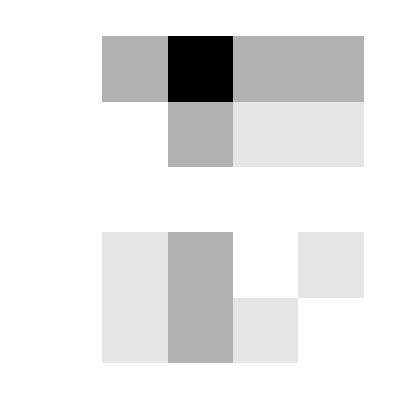
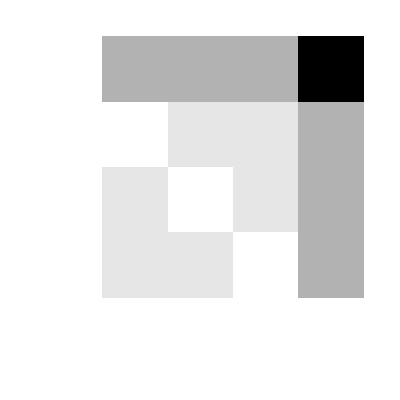
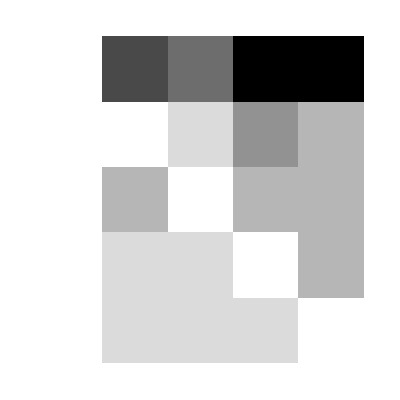
{1,-Graphics-,-Graphics-}
{2,-Graphics-,-Graphics-}
{3,-Graphics-,-Graphics-}
{4,-Graphics-,-Graphics-}
{5,-Graphics-,-Graphics-}
{6,-Graphics-,-Graphics-}
{7,-Graphics-,-Graphics-}
{8,-Graphics-,-Graphics-}
{9,-Graphics-,-Graphics-}
{10,-Graphics-,-Graphics-}
{11,-Graphics-,-Graphics-}
{12,-Graphics-,-Graphics-}
{13,-Graphics-,-Graphics-}
{14,-Graphics-,-Graphics-}
{15,-Graphics-,-Graphics-}
{16,-Graphics-,-Graphics-}
{17,-Graphics-,-Graphics-}
{18,-Graphics-,-Graphics-}
{19,-Graphics-,-Graphics-}
{20,-Graphics-,-Graphics-}
{21,-Graphics-,-Graphics-}
{22,-Graphics-,-Graphics-}
{23,-Graphics-,-Graphics-}
{24,-Graphics-,-Graphics-}
{25,-Graphics-,-Graphics-}
{26,-Graphics-,-Graphics-}
{27,-Graphics-,-Graphics-}
{28,-Graphics-,-Graphics-}
{29,-Graphics-,-Graphics-}
{30,-Graphics-,-Graphics-}
{31,-Graphics-,-Graphics-}
{32,-Graphics-,-Graphics-}
{33,-Graphics-,-Graphics-}
{34,-Graphics-,-Graphics-}
{35,-Graphics-,-Graphics-}
{36,-Graphics-,-Graphics-}
{37,-Graphics-,-Graphics-}
{38,-Graphics-,-Graphics-}
{39,-Graphics-,-Graphics-}
{40,-Graphics-,-Graphics-}
{41,-Graphics-,-Graphics-}
{42,-Graphics-,-Graphics-}
{43,-Graphics-,-Graphics-}
{44,-Graphics-,-Graphics-}
{45,-Graphics-,-Graphics-}
{46,-Graphics-,-Graphics-}
{47,-Graphics-,-Graphics-}
{48,-Graphics-,-Graphics-}
{49,-Graphics-,-Graphics-}
{50,-Graphics-,-Graphics-}
{51,-Graphics-,-Graphics-}
{52,-Graphics-,-Graphics-}
{53,-Graphics-,-Graphics-}
{54,-Graphics-,-Graphics-}
{55,-Graphics-,-Graphics-}
{56,-Graphics-,-Graphics-}
{57,-Graphics-,-Graphics-}
{58,-Graphics-,-Graphics-}
{59,-Graphics-,-Graphics-}
{60,-Graphics-,-Graphics-}
{61,-Graphics-,-Graphics-}
{62,-Graphics-,-Graphics-}
{63,-Graphics-,-Graphics-}
{64,-Graphics-,-Graphics-}
{65,-Graphics-,-Graphics-}
{66,-Graphics-,-Graphics-}
{67,-Graphics-,-Graphics-}
{68,-Graphics-,-Graphics-}
{69,-Graphics-,-Graphics-}
{70,-Graphics-,-Graphics-}
{71,-Graphics-,-Graphics-}
{72,-Graphics-,-Graphics-}
{73,-Graphics-,-Graphics-}
{74,-Graphics-,-Graphics-}
{75,-Graphics-,-Graphics-}
{76,-Graphics-,-Graphics-}
{77,-Graphics-,-Graphics-}
{78,-Graphics-,-Graphics-}
{79,-Graphics-,-Graphics-}
{80,-Graphics-,-Graphics-}
{81,-Graphics-,-Graphics-}
{82,-Graphics-,-Graphics-}
{83,-Graphics-,-Graphics-}
{84,-Graphics-,-Graphics-}
{85,-Graphics-,-Graphics-}
{86,-Graphics-,-Graphics-}
{87,-Graphics-,-Graphics-}
{88,-Graphics-,-Graphics-}
{89,-Graphics-,-Graphics-}
{90,-Graphics-,-Graphics-}
{91,-Graphics-,-Graphics-}
{92,-Graphics-,-Graphics-}
{93,-Graphics-,-Graphics-}
{94,-Graphics-,-Graphics-}
{95,-Graphics-,-Graphics-}
{96,-Graphics-,-Graphics-}
{97,-Graphics-,-Graphics-}
{98,-Graphics-,-Graphics-}
{99,-Graphics-,-Graphics-}
{100,-Graphics-,-Graphics-}
{101,-Graphics-,-Graphics-}
{102,-Graphics-,-Graphics-}
{103,-Graphics-,-Graphics-}
{104,-Graphics-,-Graphics-}
{105,-Graphics-,-Graphics-}
{106,-Graphics-,-Graphics-}
{107,-Graphics-,-Graphics-}
{108,-Graphics-,-Graphics-}
{109,-Graphics-,-Graphics-}
{110,-Graphics-,-Graphics-}
{111,-Graphics-,-Graphics-}
{112,-Graphics-,-Graphics-}
{113,-Graphics-,-Graphics-}
{114,-Graphics-,-Graphics-}
{115,-Graphics-,-Graphics-}
{116,-Graphics-,-Graphics-}
{117,-Graphics-,-Graphics-}
{118,-Graphics-,-Graphics-}
{119,-Graphics-,-Graphics-}
{120,-Graphics-,-Graphics-}
{121,-Graphics-,-Graphics-}
{122,-Graphics-,-Graphics-}
{123,-Graphics-,-Graphics-}
{124,-Graphics-,-Graphics-}
{125,-Graphics-,-Graphics-}
{126,-Graphics-,-Graphics-}
{127,-Graphics-,-Graphics-}
{128,-Graphics-,-Graphics-}
{129,-Graphics-,-Graphics-}
{130,-Graphics-,-Graphics-}
{131,-Graphics-,-Graphics-}
{132,-Graphics-,-Graphics-}
{133,-Graphics-,-Graphics-}
{134,-Graphics-,-Graphics-}
{135,-Graphics-,-Graphics-}
{136,-Graphics-,-Graphics-}
{137,-Graphics-,-Graphics-}
{138,-Graphics-,-Graphics-}
{139,-Graphics-,-Graphics-}
{140,-Graphics-,-Graphics-}
{141,-Graphics-,-Graphics-}
{142,-Graphics-,-Graphics-}
{143,-Graphics-,-Graphics-}
{144,-Graphics-,-Graphics-}
{145,-Graphics-,-Graphics-}
{146,-Graphics-,-Graphics-}
{147,-Graphics-,-Graphics-}
{148,-Graphics-,-Graphics-}
{149,-Graphics-,-Graphics-}
{150,-Graphics-,-Graphics-}
{151,-Graphics-,-Graphics-}
{152,-Graphics-,-Graphics-}
{153,-Graphics-,-Graphics-}
{154,-Graphics-,-Graphics-}
{155,-Graphics-,-Graphics-}
{156,-Graphics-,-Graphics-}
{157,-Graphics-,-Graphics-}
{158,-Graphics-,-Graphics-}
{159,-Graphics-,-Graphics-}
{160,-Graphics-,-Graphics-}
{161,-Graphics-,-Graphics-}
{162,-Graphics-,-Graphics-}
{163,-Graphics-,-Graphics-}
{164,-Graphics-,-Graphics-}
{165,-Graphics-,-Graphics-}
{166,-Graphics-,-Graphics-}
{167,-Graphics-,-Graphics-}
{168,-Graphics-,-Graphics-}
{169,-Graphics-,-Graphics-}
{170,-Graphics-,-Graphics-}
{171,-Graphics-,-Graphics-}
{172,-Graphics-,-Graphics-}
{173,-Graphics-,-Graphics-}
{174,-Graphics-,-Graphics-}
{175,-Graphics-,-Graphics-}
{176,-Graphics-,-Graphics-}
{177,-Graphics-,-Graphics-}
{178,-Graphics-,-Graphics-}
{179,-Graphics-,-Graphics-}
{180,-Graphics-,-Graphics-}
{181,-Graphics-,-Graphics-}
{182,-Graphics-,-Graphics-}
{183,-Graphics-,-Graphics-}
{184,-Graphics-,-Graphics-}
{185,-Graphics-,-Graphics-}
{186,-Graphics-,-Graphics-}
{187,-Graphics-,-Graphics-}
{188,-Graphics-,-Graphics-}
{189,-Graphics-,-Graphics-}
{190,-Graphics-,-Graphics-}
{191,-Graphics-,-Graphics-}
{192,-Graphics-,-Graphics-}
{193,-Graphics-,-Graphics-}
{194,-Graphics-,-Graphics-}
{195,-Graphics-,-Graphics-}
{196,-Graphics-,-Graphics-}
{197,-Graphics-,-Graphics-}
{198,-Graphics-,-Graphics-}
{199,-Graphics-,-Graphics-}
{200,-Graphics-,-Graphics-}
{201,-Graphics-,-Graphics-}
{202,-Graphics-,-Graphics-}
{203,-Graphics-,-Graphics-}
{204,-Graphics-,-Graphics-}
{205,-Graphics-,-Graphics-}
{206,-Graphics-,-Graphics-}
{207,-Graphics-,-Graphics-}
{208,-Graphics-,-Graphics-}
{209,-Graphics-,-Graphics-}
{210,-Graphics-,-Graphics-}
{211,-Graphics-,-Graphics-}
{212,-Graphics-,-Graphics-}
{213,-Graphics-,-Graphics-}
{214,-Graphics-,-Graphics-}
{215,-Graphics-,-Graphics-}
{216,-Graphics-,-Graphics-}
{217,-Graphics-,-Graphics-}
{218,-Graphics-,-Graphics-}
{219,-Graphics-,-Graphics-}
{220,-Graphics-,-Graphics-}
{221,-Graphics-,-Graphics-}
{222,-Graphics-,-Graphics-}
{223,-Graphics-,-Graphics-}
{224,-Graphics-,-Graphics-}
{225,-Graphics-,-Graphics-}
{226,-Graphics-,-Graphics-}
{227,-Graphics-,-Graphics-}
{228,-Graphics-,-Graphics-}
{229,-Graphics-,-Graphics-}
{230,-Graphics-,-Graphics-}
{231,-Graphics-,-Graphics-}
{232,-Graphics-,-Graphics-}
{233,-Graphics-,-Graphics-}
{234,-Graphics-,-Graphics-}
{235,-Graphics-,-Graphics-}
{236,-Graphics-,-Graphics-}
{237,-Graphics-,-Graphics-}
{238,-Graphics-,-Graphics-}
{239,-Graphics-,-Graphics-}
{240,-Graphics-,-Graphics-}
{241,-Graphics-,-Graphics-}
{242,-Graphics-,-Graphics-}
{243,-Graphics-,-Graphics-}
{244,-Graphics-,-Graphics-}
{245,-Graphics-,-Graphics-}
{246,-Graphics-,-Graphics-}
{247,-Graphics-,-Graphics-}
{248,-Graphics-,-Graphics-}
{249,-Graphics-,-Graphics-}
{250,-Graphics-,-Graphics-}
{251,-Graphics-,-Graphics-}
{252,-Graphics-,-Graphics-}
{253,-Graphics-,-Graphics-}
{254,-Graphics-,-Graphics-}
{255,-Graphics-,-Graphics-}
{256,-Graphics-,-Graphics-}
{257,-Graphics-,-Graphics-}
{258,-Graphics-,-Graphics-}
{259,-Graphics-,-Graphics-}
{260,-Graphics-,-Graphics-}
{261,-Graphics-,-Graphics-}
{262,-Graphics-,-Graphics-}
{263,-Graphics-,-Graphics-}
{264,-Graphics-,-Graphics-}
{265,-Graphics-,-Graphics-}
{266,-Graphics-,-Graphics-}
{267,-Graphics-,-Graphics-}
{268,-Graphics-,-Graphics-}
{269,-Graphics-,-Graphics-}
{270,-Graphics-,-Graphics-}
{271,-Graphics-,-Graphics-}
{272,-Graphics-,-Graphics-}
{273,-Graphics-,-Graphics-}
{274,-Graphics-,-Graphics-}
{275,-Graphics-,-Graphics-}
{276,-Graphics-,-Graphics-}
{277,-Graphics-,-Graphics-}
{278,-Graphics-,-Graphics-}
{279,-Graphics-,-Graphics-}
{280,-Graphics-,-Graphics-}
{281,-Graphics-,-Graphics-}
{282,-Graphics-,-Graphics-}
{283,-Graphics-,-Graphics-}
{284,-Graphics-,-Graphics-}
{285,-Graphics-,-Graphics-}
{286,-Graphics-,-Graphics-}
{287,-Graphics-,-Graphics-}
{288,-Graphics-,-Graphics-}
{289,-Graphics-,-Graphics-}
{290,-Graphics-,-Graphics-}
{291,-Graphics-,-Graphics-}
{292,-Graphics-,-Graphics-}
{293,-Graphics-,-Graphics-}
{294,-Graphics-,-Graphics-}
{295,-Graphics-,-Graphics-}
{296,-Graphics-,-Graphics-}
{297,-Graphics-,-Graphics-}
{298,-Graphics-,-Graphics-}
{299,-Graphics-,-Graphics-}
{300,-Graphics-,-Graphics-}
{301,-Graphics-,-Graphics-}
{302,-Graphics-,-Graphics-}
{303,-Graphics-,-Graphics-}
{304,-Graphics-,-Graphics-}
{305,-Graphics-,-Graphics-}
{306,-Graphics-,-Graphics-}
{307,-Graphics-,-Graphics-}
{308,-Graphics-,-Graphics-}
{309,-Graphics-,-Graphics-}
{310,-Graphics-,-Graphics-}
{311,-Graphics-,-Graphics-}
{312,-Graphics-,-Graphics-}
{313,-Graphics-,-Graphics-}
{314,-Graphics-,-Graphics-}
{315,-Graphics-,-Graphics-}
{316,-Graphics-,-Graphics-}
{317,-Graphics-,-Graphics-}
{318,-Graphics-,-Graphics-}
{319,-Graphics-,-Graphics-}
{320,-Graphics-,-Graphics-}
{321,-Graphics-,-Graphics-}
{322,-Graphics-,-Graphics-}
{323,-Graphics-,-Graphics-}
{324,-Graphics-,-Graphics-}
{325,-Graphics-,-Graphics-}
{326,-Graphics-,-Graphics-}
{327,-Graphics-,-Graphics-}
{328,-Graphics-,-Graphics-}
{329,-Graphics-,-Graphics-}
{330,-Graphics-,-Graphics-}
{331,-Graphics-,-Graphics-}
{332,-Graphics-,-Graphics-}
{333,-Graphics-,-Graphics-}
{334,-Graphics-,-Graphics-}
{335,-Graphics-,-Graphics-}
{336,-Graphics-,-Graphics-}
{337,-Graphics-,-Graphics-}
{338,-Graphics-,-Graphics-}
{339,-Graphics-,-Graphics-}
{340,-Graphics-,-Graphics-}
{341,-Graphics-,-Graphics-}
{342,-Graphics-,-Graphics-}
{343,-Graphics-,-Graphics-}
{344,-Graphics-,-Graphics-}
{345,-Graphics-,-Graphics-}
{346,-Graphics-,-Graphics-}
{347,-Graphics-,-Graphics-}
{348,-Graphics-,-Graphics-}
{349,-Graphics-,-Graphics-}
{350,-Graphics-,-Graphics-}
{351,-Graphics-,-Graphics-}
{352,-Graphics-,-Graphics-}
{353,-Graphics-,-Graphics-}
{354,-Graphics-,-Graphics-}
{355,-Graphics-,-Graphics-}
{356,-Graphics-,-Graphics-}
{357,-Graphics-,-Graphics-}
{358,-Graphics-,-Graphics-}
{359,-Graphics-,-Graphics-}
{360,-Graphics-,-Graphics-}
{361,-Graphics-,-Graphics-}
{362,-Graphics-,-Graphics-}
{363,-Graphics-,-Graphics-}
{364,-Graphics-,-Graphics-}
{365,-Graphics-,-Graphics-}
{366,-Graphics-,-Graphics-}
{367,-Graphics-,-Graphics-}
{368,-Graphics-,-Graphics-}
{369,-Graphics-,-Graphics-}
{370,-Graphics-,-Graphics-}
{371,-Graphics-,-Graphics-}
{372,-Graphics-,-Graphics-}
{373,-Graphics-,-Graphics-}
{374,-Graphics-,-Graphics-}
{375,-Graphics-,-Graphics-}
{376,-Graphics-,-Graphics-}
{377,-Graphics-,-Graphics-}
{378,-Graphics-,-Graphics-}
{379,-Graphics-,-Graphics-}
{380,-Graphics-,-Graphics-}
{381,-Graphics-,-Graphics-}
{382,-Graphics-,-Graphics-}
{383,-Graphics-,-Graphics-}
{384,-Graphics-,-Graphics-}
{385,-Graphics-,-Graphics-}
{386,-Graphics-,-Graphics-}
{387,-Graphics-,-Graphics-}
{388,-Graphics-,-Graphics-}
{389,-Graphics-,-Graphics-}
{390,-Graphics-,-Graphics-}
{391,-Graphics-,-Graphics-}
{392,-Graphics-,-Graphics-}
{393,-Graphics-,-Graphics-}
{394,-Graphics-,-Graphics-}
{395,-Graphics-,-Graphics-}
{396,-Graphics-,-Graphics-}
{397,-Graphics-,-Graphics-}
{398,-Graphics-,-Graphics-}
{399,-Graphics-,-Graphics-}
{400,-Graphics-,-Graphics-}
{401,-Graphics-,-Graphics-}
{402,-Graphics-,-Graphics-}
{403,-Graphics-,-Graphics-}
{404,-Graphics-,-Graphics-}
{405,-Graphics-,-Graphics-}
{406,-Graphics-,-Graphics-}
{407,-Graphics-,-Graphics-}
{408,-Graphics-,-Graphics-}
{409,-Graphics-,-Graphics-}
{410,-Graphics-,-Graphics-}
{411,-Graphics-,-Graphics-}
{412,-Graphics-,-Graphics-}
{413,-Graphics-,-Graphics-}
{414,-Graphics-,-Graphics-}
{415,-Graphics-,-Graphics-}
{416,-Graphics-,-Graphics-}
{417,-Graphics-,-Graphics-}
{418,-Graphics-,-Graphics-}
{419,-Graphics-,-Graphics-}
{420,-Graphics-,-Graphics-}
{421,-Graphics-,-Graphics-}
{422,-Graphics-,-Graphics-}
{423,-Graphics-,-Graphics-}
{424,-Graphics-,-Graphics-}
{425,-Graphics-,-Graphics-}
{426,-Graphics-,-Graphics-}
{427,-Graphics-,-Graphics-}
{428,-Graphics-,-Graphics-}
{429,-Graphics-,-Graphics-}
{430,-Graphics-,-Graphics-}
{431,-Graphics-,-Graphics-}
{432,-Graphics-,-Graphics-}
{433,-Graphics-,-Graphics-}
{434,-Graphics-,-Graphics-}
{435,-Graphics-,-Graphics-}
{436,-Graphics-,-Graphics-}
{437,-Graphics-,-Graphics-}
{438,-Graphics-,-Graphics-}
{439,-Graphics-,-Graphics-}
{440,-Graphics-,-Graphics-}
{441,-Graphics-,-Graphics-}
{442,-Graphics-,-Graphics-}
{443,-Graphics-,-Graphics-}
{444,-Graphics-,-Graphics-}
{445,-Graphics-,-Graphics-}
{446,-Graphics-,-Graphics-}
{447,-Graphics-,-Graphics-}
{448,-Graphics-,-Graphics-}
{449,-Graphics-,-Graphics-}
{450,-Graphics-,-Graphics-}
{451,-Graphics-,-Graphics-}
{452,-Graphics-,-Graphics-}
{453,-Graphics-,-Graphics-}
{454,-Graphics-,-Graphics-}
{455,-Graphics-,-Graphics-}
{456,-Graphics-,-Graphics-}
{457,-Graphics-,-Graphics-}
{458,-Graphics-,-Graphics-}
{459,-Graphics-,-Graphics-}
{460,-Graphics-,-Graphics-}
{461,-Graphics-,-Graphics-}
{462,-Graphics-,-Graphics-}
{463,-Graphics-,-Graphics-}
{464,-Graphics-,-Graphics-}
{465,-Graphics-,-Graphics-}
{466,-Graphics-,-Graphics-}
{467,-Graphics-,-Graphics-}
{468,-Graphics-,-Graphics-}
{469,-Graphics-,-Graphics-}
{470,-Graphics-,-Graphics-}
{471,-Graphics-,-Graphics-}
{472,-Graphics-,-Graphics-}
{473,-Graphics-,-Graphics-}
{474,-Graphics-,-Graphics-}
{475,-Graphics-,-Graphics-}
{476,-Graphics-,-Graphics-}
{477,-Graphics-,-Graphics-}
{478,-Graphics-,-Graphics-}
{479,-Graphics-,-Graphics-}
{480,-Graphics-,-Graphics-}
{481,-Graphics-,-Graphics-}
{482,-Graphics-,-Graphics-}
{483,-Graphics-,-Graphics-}
{484,-Graphics-,-Graphics-}
{485,-Graphics-,-Graphics-}
{486,-Graphics-,-Graphics-}
{487,-Graphics-,-Graphics-}
{488,-Graphics-,-Graphics-}
{489,-Graphics-,-Graphics-}
{490,-Graphics-,-Graphics-}
{491,-Graphics-,-Graphics-}
{492,-Graphics-,-Graphics-}
{493,-Graphics-,-Graphics-}
{494,-Graphics-,-Graphics-}
{495,-Graphics-,-Graphics-}
{496,-Graphics-,-Graphics-}
{497,-Graphics-,-Graphics-}
{498,-Graphics-,-Graphics-}
{499,-Graphics-,-Graphics-}
{500,-Graphics-,-Graphics-}
{501,-Graphics-,-Graphics-}
{502,-Graphics-,-Graphics-}
{503,-Graphics-,-Graphics-}
{504,-Graphics-,-Graphics-}
{505,-Graphics-,-Graphics-}
{506,-Graphics-,-Graphics-}
{507,-Graphics-,-Graphics-}
{508,-Graphics-,-Graphics-}
{509,-Graphics-,-Graphics-}
{510,-Graphics-,-Graphics-}
{511,-Graphics-,-Graphics-}
{512,-Graphics-,-Graphics-}
{513,-Graphics-,-Graphics-}
{514,-Graphics-,-Graphics-}
{515,-Graphics-,-Graphics-}
{516,-Graphics-,-Graphics-}
{517,-Graphics-,-Graphics-}
{518,-Graphics-,-Graphics-}
{519,-Graphics-,-Graphics-}
{520,-Graphics-,-Graphics-}
{521,-Graphics-,-Graphics-}
{522,-Graphics-,-Graphics-}
{523,-Graphics-,-Graphics-}
{524,-Graphics-,-Graphics-}
{525,-Graphics-,-Graphics-}
{526,-Graphics-,-Graphics-}
{527,-Graphics-,-Graphics-}
{528,-Graphics-,-Graphics-}
{529,-Graphics-,-Graphics-}
{530,-Graphics-,-Graphics-}
{531,-Graphics-,-Graphics-}
{532,-Graphics-,-Graphics-}
{533,-Graphics-,-Graphics-}
{534,-Graphics-,-Graphics-}
{535,-Graphics-,-Graphics-}
{536,-Graphics-,-Graphics-}
{537,-Graphics-,-Graphics-}
{538,-Graphics-,-Graphics-}
{539,-Graphics-,-Graphics-}
{540,-Graphics-,-Graphics-}
{541,-Graphics-,-Graphics-}
{542,-Graphics-,-Graphics-}
{543,-Graphics-,-Graphics-}
{544,-Graphics-,-Graphics-}
{545,-Graphics-,-Graphics-}
{546,-Graphics-,-Graphics-}
{547,-Graphics-,-Graphics-}
{548,-Graphics-,-Graphics-}
{549,-Graphics-,-Graphics-}
{550,-Graphics-,-Graphics-}
{551,-Graphics-,-Graphics-}
{552,-Graphics-,-Graphics-}
{553,-Graphics-,-Graphics-}
{554,-Graphics-,-Graphics-}
{555,-Graphics-,-Graphics-}
{556,-Graphics-,-Graphics-}
{557,-Graphics-,-Graphics-}
{558,-Graphics-,-Graphics-}
{559,-Graphics-,-Graphics-}
{560,-Graphics-,-Graphics-}
{561,-Graphics-,-Graphics-}
{562,-Graphics-,-Graphics-}
{563,-Graphics-,-Graphics-}
{564,-Graphics-,-Graphics-}
{565,-Graphics-,-Graphics-}
{566,-Graphics-,-Graphics-}
{567,-Graphics-,-Graphics-}
{568,-Graphics-,-Graphics-}
{569,-Graphics-,-Graphics-}
{570,-Graphics-,-Graphics-}
{571,-Graphics-,-Graphics-}
{572,-Graphics-,-Graphics-}
{573,-Graphics-,-Graphics-}
{574,-Graphics-,-Graphics-}
{575,-Graphics-,-Graphics-}
{576,-Graphics-,-Graphics-}
{577,-Graphics-,-Graphics-}
{578,-Graphics-,-Graphics-}
{579,-Graphics-,-Graphics-}
{580,-Graphics-,-Graphics-}
{581,-Graphics-,-Graphics-}
{582,-Graphics-,-Graphics-}
{583,-Graphics-,-Graphics-}
{584,-Graphics-,-Graphics-}
{585,-Graphics-,-Graphics-}
{586,-Graphics-,-Graphics-}
{587,-Graphics-,-Graphics-}
{588,-Graphics-,-Graphics-}
{589,-Graphics-,-Graphics-}
{590,-Graphics-,-Graphics-}
{591,-Graphics-,-Graphics-}
{592,-Graphics-,-Graphics-}
{593,-Graphics-,-Graphics-}
{594,-Graphics-,-Graphics-}
{595,-Graphics-,-Graphics-}
{596,-Graphics-,-Graphics-}
{597,-Graphics-,-Graphics-}
{598,-Graphics-,-Graphics-}
{599,-Graphics-,-Graphics-}
{600,-Graphics-,-Graphics-}
{601,-Graphics-,-Graphics-}
{602,-Graphics-,-Graphics-}
{603,-Graphics-,-Graphics-}
{604,-Graphics-,-Graphics-}
{605,-Graphics-,-Graphics-}
{606,-Graphics-,-Graphics-}
{607,-Graphics-,-Graphics-}
{608,-Graphics-,-Graphics-}
{609,-Graphics-,-Graphics-}
{610,-Graphics-,-Graphics-}
{611,-Graphics-,-Graphics-}
{612,-Graphics-,-Graphics-}
{613,-Graphics-,-Graphics-}
{614,-Graphics-,-Graphics-}
{615,-Graphics-,-Graphics-}
{616,-Graphics-,-Graphics-}
{617,-Graphics-,-Graphics-}
{618,-Graphics-,-Graphics-}
{619,-Graphics-,-Graphics-}
{620,-Graphics-,-Graphics-}
{621,-Graphics-,-Graphics-}
{622,-Graphics-,-Graphics-}
{623,-Graphics-,-Graphics-}
{624,-Graphics-,-Graphics-}
{625,-Graphics-,-Graphics-}
{626,-Graphics-,-Graphics-}
{627,-Graphics-,-Graphics-}
{628,-Graphics-,-Graphics-}
{629,-Graphics-,-Graphics-}
{630,-Graphics-,-Graphics-}
{631,-Graphics-,-Graphics-}
{632,-Graphics-,-Graphics-}
{633,-Graphics-,-Graphics-}
{634,-Graphics-,-Graphics-}
{635,-Graphics-,-Graphics-}
{636,-Graphics-,-Graphics-}
{637,-Graphics-,-Graphics-}
{638,-Graphics-,-Graphics-}
{639,-Graphics-,-Graphics-}
{640,-Graphics-,-Graphics-}
{641,-Graphics-,-Graphics-}
{642,-Graphics-,-Graphics-}
{643,-Graphics-,-Graphics-}
{644,-Graphics-,-Graphics-}
{645,-Graphics-,-Graphics-}
{646,-Graphics-,-Graphics-}
{647,-Graphics-,-Graphics-}
{648,-Graphics-,-Graphics-}
{649,-Graphics-,-Graphics-}
{650,-Graphics-,-Graphics-}
{651,-Graphics-,-Graphics-}
{652,-Graphics-,-Graphics-}
{653,-Graphics-,-Graphics-}
{654,-Graphics-,-Graphics-}
{655,-Graphics-,-Graphics-}
{656,-Graphics-,-Graphics-}
{657,-Graphics-,-Graphics-}
{658,-Graphics-,-Graphics-}
{659,-Graphics-,-Graphics-}
{660,-Graphics-,-Graphics-}
{661,-Graphics-,-Graphics-}
{662,-Graphics-,-Graphics-}
{663,-Graphics-,-Graphics-}
{664,-Graphics-,-Graphics-}
{665,-Graphics-,-Graphics-}
{666,-Graphics-,-Graphics-}
{667,-Graphics-,-Graphics-}
{668,-Graphics-,-Graphics-}
{669,-Graphics-,-Graphics-}
{670,-Graphics-,-Graphics-}
{671,-Graphics-,-Graphics-}
{672,-Graphics-,-Graphics-}
{673,-Graphics-,-Graphics-}
{674,-Graphics-,-Graphics-}
{675,-Graphics-,-Graphics-}
{676,-Graphics-,-Graphics-}
{677,-Graphics-,-Graphics-}
{678,-Graphics-,-Graphics-}
{679,-Graphics-,-Graphics-}
{680,-Graphics-,-Graphics-}
{681,-Graphics-,-Graphics-}
{682,-Graphics-,-Graphics-}
{683,-Graphics-,-Graphics-}
{684,-Graphics-,-Graphics-}
{685,-Graphics-,-Graphics-}
{686,-Graphics-,-Graphics-}
{687,-Graphics-,-Graphics-}
{688,-Graphics-,-Graphics-}
{689,-Graphics-,-Graphics-}
{690,-Graphics-,-Graphics-}
{691,-Graphics-,-Graphics-}
{692,-Graphics-,-Graphics-}
{693,-Graphics-,-Graphics-}
{694,-Graphics-,-Graphics-}
{695,-Graphics-,-Graphics-}
{696,-Graphics-,-Graphics-}
{697,-Graphics-,-Graphics-}
{698,-Graphics-,-Graphics-}
{699,-Graphics-,-Graphics-}
{700,-Graphics-,-Graphics-}
{701,-Graphics-,-Graphics-}
{702,-Graphics-,-Graphics-}
{703,-Graphics-,-Graphics-}
{704,-Graphics-,-Graphics-}
{705,-Graphics-,-Graphics-}
{706,-Graphics-,-Graphics-}
{707,-Graphics-,-Graphics-}
{708,-Graphics-,-Graphics-}
{709,-Graphics-,-Graphics-}
{710,-Graphics-,-Graphics-}
{711,-Graphics-,-Graphics-}
{712,-Graphics-,-Graphics-}
{713,-Graphics-,-Graphics-}
{714,-Graphics-,-Graphics-}
{715,-Graphics-,-Graphics-}
{716,-Graphics-,-Graphics-}
{717,-Graphics-,-Graphics-}
{718,-Graphics-,-Graphics-}
{719,-Graphics-,-Graphics-}
{720,-Graphics-,-Graphics-}
{721,-Graphics-,-Graphics-}
{722,-Graphics-,-Graphics-}
{723,-Graphics-,-Graphics-}
{724,-Graphics-,-Graphics-}
{725,-Graphics-,-Graphics-}
{726,-Graphics-,-Graphics-}
{727,-Graphics-,-Graphics-}
{728,-Graphics-,-Graphics-}
{729,-Graphics-,-Graphics-}
{730,-Graphics-,-Graphics-}
{731,-Graphics-,-Graphics-}
{732,-Graphics-,-Graphics-}
{733,-Graphics-,-Graphics-}
{734,-Graphics-,-Graphics-}
{735,-Graphics-,-Graphics-}
{736,-Graphics-,-Graphics-}
{737,-Graphics-,-Graphics-}
{738,-Graphics-,-Graphics-}
{739,-Graphics-,-Graphics-}
{740,-Graphics-,-Graphics-}
{741,-Graphics-,-Graphics-}
{742,-Graphics-,-Graphics-}
{743,-Graphics-,-Graphics-}
{744,-Graphics-,-Graphics-}
{745,-Graphics-,-Graphics-}
{746,-Graphics-,-Graphics-}
{747,-Graphics-,-Graphics-}
{748,-Graphics-,-Graphics-}
{749,-Graphics-,-Graphics-}
{750,-Graphics-,-Graphics-}
{751,-Graphics-,-Graphics-}
{752,-Graphics-,-Graphics-}
{753,-Graphics-,-Graphics-}
{754,-Graphics-,-Graphics-}
{755,-Graphics-,-Graphics-}
{756,-Graphics-,-Graphics-}
{757,-Graphics-,-Graphics-}
{758,-Graphics-,-Graphics-}
{759,-Graphics-,-Graphics-}
{760,-Graphics-,-Graphics-}
{761,-Graphics-,-Graphics-}
{762,-Graphics-,-Graphics-}
{763,-Graphics-,-Graphics-}
{764,-Graphics-,-Graphics-}
{765,-Graphics-,-Graphics-}
{766,-Graphics-,-Graphics-}
{767,-Graphics-,-Graphics-}
{768,-Graphics-,-Graphics-}
{769,-Graphics-,-Graphics-}
{770,-Graphics-,-Graphics-}
{771,-Graphics-,-Graphics-}
{772,-Graphics-,-Graphics-}
{773,-Graphics-,-Graphics-}
{774,-Graphics-,-Graphics-}
{775,-Graphics-,-Graphics-}
{776,-Graphics-,-Graphics-}
{777,-Graphics-,-Graphics-}
{778,-Graphics-,-Graphics-}
{779,-Graphics-,-Graphics-}
{780,-Graphics-,-Graphics-}
{781,-Graphics-,-Graphics-}
{782,-Graphics-,-Graphics-}
{783,-Graphics-,-Graphics-}
{784,-Graphics-,-Graphics-}
{785,-Graphics-,-Graphics-}
{786,-Graphics-,-Graphics-}
{787,-Graphics-,-Graphics-}
{788,-Graphics-,-Graphics-}
{789,-Graphics-,-Graphics-}
{790,-Graphics-,-Graphics-}
{791,-Graphics-,-Graphics-}
{792,-Graphics-,-Graphics-}
{793,-Graphics-,-Graphics-}
{794,-Graphics-,-Graphics-}
{795,-Graphics-,-Graphics-}
{796,-Graphics-,-Graphics-}
{797,-Graphics-,-Graphics-}
{798,-Graphics-,-Graphics-}
{799,-Graphics-,-Graphics-}
{800,-Graphics-,-Graphics-}
{801,-Graphics-,-Graphics-}
{802,-Graphics-,-Graphics-}
{803,-Graphics-,-Graphics-}
{804,-Graphics-,-Graphics-}
{805,-Graphics-,-Graphics-}
{806,-Graphics-,-Graphics-}
{807,-Graphics-,-Graphics-}
{808,-Graphics-,-Graphics-}
{809,-Graphics-,-Graphics-}
{810,-Graphics-,-Graphics-}
{811,-Graphics-,-Graphics-}
{812,-Graphics-,-Graphics-}
{813,-Graphics-,-Graphics-}
{814,-Graphics-,-Graphics-}
{815,-Graphics-,-Graphics-}
{816,-Graphics-,-Graphics-}
{817,-Graphics-,-Graphics-}
{818,-Graphics-,-Graphics-}
{819,-Graphics-,-Graphics-}
{820,-Graphics-,-Graphics-}
{821,-Graphics-,-Graphics-}
{822,-Graphics-,-Graphics-}
{823,-Graphics-,-Graphics-}
{824,-Graphics-,-Graphics-}
{825,-Graphics-,-Graphics-}
{826,-Graphics-,-Graphics-}
{827,-Graphics-,-Graphics-}
{828,-Graphics-,-Graphics-}
{829,-Graphics-,-Graphics-}
{830,-Graphics-,-Graphics-}
{831,-Graphics-,-Graphics-}
{832,-Graphics-,-Graphics-}
{833,-Graphics-,-Graphics-}
{834,-Graphics-,-Graphics-}
{835,-Graphics-,-Graphics-}
{836,-Graphics-,-Graphics-}
{837,-Graphics-,-Graphics-}
{838,-Graphics-,-Graphics-}
{839,-Graphics-,-Graphics-}
{840,-Graphics-,-Graphics-}
{841,-Graphics-,-Graphics-}
{842,-Graphics-,-Graphics-}
{843,-Graphics-,-Graphics-}
{844,-Graphics-,-Graphics-}
{845,-Graphics-,-Graphics-}
{846,-Graphics-,-Graphics-}
{847,-Graphics-,-Graphics-}
{848,-Graphics-,-Graphics-}
{849,-Graphics-,-Graphics-}
{850,-Graphics-,-Graphics-}
{851,-Graphics-,-Graphics-}
{852,-Graphics-,-Graphics-}
{853,-Graphics-,-Graphics-}
{854,-Graphics-,-Graphics-}
{855,-Graphics-,-Graphics-}
{856,-Graphics-,-Graphics-}
{857,-Graphics-,-Graphics-}
{858,-Graphics-,-Graphics-}
{859,-Graphics-,-Graphics-}
{860,-Graphics-,-Graphics-}
{861,-Graphics-,-Graphics-}
{862,-Graphics-,-Graphics-}
{863,-Graphics-,-Graphics-}
{864,-Graphics-,-Graphics-}
{865,-Graphics-,-Graphics-}
{866,-Graphics-,-Graphics-}
{867,-Graphics-,-Graphics-}
{868,-Graphics-,-Graphics-}
{869,-Graphics-,-Graphics-}
{870,-Graphics-,-Graphics-}
{871,-Graphics-,-Graphics-}
{872,-Graphics-,-Graphics-}
{873,-Graphics-,-Graphics-}
{874,-Graphics-,-Graphics-}
{875,-Graphics-,-Graphics-}
{876,-Graphics-,-Graphics-}
{877,-Graphics-,-Graphics-}
{878,-Graphics-,-Graphics-}
{879,-Graphics-,-Graphics-}
{880,-Graphics-,-Graphics-}
{881,-Graphics-,-Graphics-}
{882,-Graphics-,-Graphics-}
{883,-Graphics-,-Graphics-}
{884,-Graphics-,-Graphics-}
{885,-Graphics-,-Graphics-}
{886,-Graphics-,-Graphics-}
{887,-Graphics-,-Graphics-}
{888,-Graphics-,-Graphics-}
{889,-Graphics-,-Graphics-}
{890,-Graphics-,-Graphics-}
{891,-Graphics-,-Graphics-}
{892,-Graphics-,-Graphics-}
{893,-Graphics-,-Graphics-}
{894,-Graphics-,-Graphics-}
{895,-Graphics-,-Graphics-}
{896,-Graphics-,-Graphics-}
{897,-Graphics-,-Graphics-}
{898,-Graphics-,-Graphics-}
{899,-Graphics-,-Graphics-}
{900,-Graphics-,-Graphics-}
{901,-Graphics-,-Graphics-}
{902,-Graphics-,-Graphics-}
{903,-Graphics-,-Graphics-}
{904,-Graphics-,-Graphics-}

```mathematica
Map[{#[[1]],ArrayPlot[#[[2]]],ArrayPlot[#[[3]]]}&,ec5s]//Column
```